```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataϕe={{0.0011477260447678,0.1672645025840688},{0.0012368241145099,0.1671455376234078},{0.0013199887388915,0.1670819487514157},{0.0014025915371377,0.1670236043781129},{0.0014851397431153,0.1669657696567420},{0.0015676826223403,0.1669079846645435},{0.0016502249815356,0.1668502045272147},{0.0017327672899592,0.1667924248638790},{0.0018153095934258,0.1667346452468207},{0.0018978518964084,0.1666768656342806},{0.0019803941993438,0.1666190860221818},{0.0020629365022745,0.1665613064101259},{0.0021454788052048,0.1665035267980743},{0.0022280211081351,0.1664457471860231},{0.0023105634110654,0.1663879675739719},{0.0023931057139956,0.1663301879619207},{0.0024756480169259,0.1662724083498695},{0.0025581903198561,0.1662146287378184},{0.0026407326227864,0.1661568491257672},{0.0027232749257166,0.1660990695137160},{0.0028058172286469,0.1660412899016648},{0.0028883595315771,0.1659835102896137},{0.0029709018345074,0.1659257306775625},{0.0030534441374376,0.1658679510655113},{0.0031359864403679,0.1658101714534601},{0.0032185287432981,0.1657523918414090},{0.0033010710462284,0.1656946122293578},{0.0033836133491586,0.1656368326173066},{0.0034661556520889,0.1655790530052554},{0.0035486979550191,0.1655212733932042},{0.0036312402579494,0.1654634937811531},{0.0037137825608796,0.1654057141691019},{0.0037963248638099,0.1653479345570507},{0.0038788671667401,0.1652901549449995},{0.0039614094696704,0.1652323753329484},{0.0040439517726006,0.1651745957208972},{0.0041264940755309,0.1651168161088460},{0.0042090363784611,0.1650590364967948},{0.0042915786813914,0.1650012568847437},{0.0043741209843216,0.1649434772726925},{0.0044566632872519,0.1648856976606413},{0.0045392055901821,0.1648279180485901},{0.0046217478931124,0.1647701384365390},{0.0047042901960426,0.1647123588244878},{0.0047868324989729,0.1646545792124366},{0.0048693748019031,0.1645967996003854},{0.0049519171048334,0.1645390199883343},{0.0050344594077637,0.1644812403762831},{0.0051170017106939,0.1644234607642319},{0.0051995440136242,0.1643656811521807},{0.0052820863165544,0.1643079015401295},{0.0053646286194847,0.1642501219280784},{0.0054471709224149,0.1641923423160272},{0.0055297132253452,0.1641345627039760},{0.0056122555282754,0.1640767830919248},{0.0056947978312057,0.1640190034798737},{0.0057773401341359,0.1639612238678225},{0.0058598824370662,0.1639034442557713},{0.0059424247399964,0.1638456646437201},{0.0060249670429267,0.1637878850316690},{0.0061075093458569,0.1637301054196178},{0.0061900516487872,0.1636723258075666},{0.0062725939517174,0.1636145461955154},{0.0063551362546477,0.1635567665834643},{0.0064376785575779,0.1634989869714131},{0.0065202208605082,0.1634412073593619},{0.0066027631634384,0.1633834277473107},{0.0066853054663687,0.1633256481352596},{0.0067678477692990,0.1632678685232084},{0.0068503900722292,0.1632100889111572},{0.0069329323751594,0.1631523092991060},{0.0070154746780897,0.1630945296870548},{0.0070980169810200,0.1630367500750037},{0.0071805592839502,0.1629789704629525},{0.0072631015868805,0.1629211908509013},{0.0073456438898107,0.1628634112388501},{0.0074281861927409,0.1628056316267990},{0.0075107284956712,0.1627478520147478},{0.0075932707986014,0.1626900724026966},{0.0076758131015317,0.1626322927906454},{0.0077583554044620,0.1625745131785943},{0.0078408977073922,0.1625167335665431},{0.0079234400103225,0.1624589539544919},{0.0080059823132527,0.1624011743424407},{0.0080885246161830,0.1623433947303896},{0.0081710669191132,0.1622856151183384},{0.0082536092220435,0.1622278355062872},{0.0083361515249737,0.1621700558942360},{0.0084186938279040,0.1621122762821849},{0.0085012361308342,0.1620544966701337},{0.0085837784337645,0.1619967170580825},{0.0086663207366947,0.1619389374460313},{0.0087488630396250,0.1618811578339802},{0.0088314053425552,0.1618233782219290},{0.0089139476454855,0.1617655986098778},{0.0089964899484157,0.1617078189978266},{0.0090790322513460,0.1616500393857755},{0.0091615745542762,0.1615922597737243},{0.0092441168572065,0.1615344801616731},{0.0093266591601368,0.1614767005496219},{0.0094092014630670,0.1614189209375708}};



dataϕep={{0.0011477260447678,0.1672645025840688},{0.0012368241145099,0.1671455376234078},{0.0013199887388915,0.1670819487514157},{0.0014025915371377,0.1670236043781129},{0.0014851397431153,0.1669657696567420},{0.0015676826223403,0.1669079846645435},{0.0016502249815356,0.1668502045272147},{0.0017327672899592,0.1667924248638790},{0.0018153095934258,0.1667346452468207},{0.0018978518964084,0.1666768656342806},{0.0019803941993438,0.1666190860221818},{0.0020629365022745,0.1665613064101259},{0.0021454788052048,0.1665035267980743},{0.0022280211081351,0.1664457471860231},{0.0023105634110654,0.1663879675739719},{0.0023931057139956,0.1663301879619207},{0.0024756480169259,0.1662724083498695},{0.0025581903198561,0.1662146287378184},{0.0026407326227864,0.1661568491257672},{0.0027232749257166,0.1660990695137160},{0.0028058172286469,0.1660412899016648},{0.0028883595315771,0.1659835102896137},{0.0029709018345074,0.1659257306775625},{0.0030534441374376,0.1658679510655113},{0.0031359864403679,0.1658101714534601},{0.0032185287432981,0.1657523918414090},{0.0033010710462284,0.1656946122293578},{0.0036258439053179,0.1656070930575793},{0.0040025885239901,0.1655105635387832},{0.0043787332694683,0.1654133093144837},{0.0047539629111928,0.1653161156409600},{0.0051282916375709,0.1652190539043320},{0.0055017631737858,0.1651221247768816},{0.0058744212955866,0.1650253221956470},{0.0062463070940910,0.1649286398304504},{0.0066174589264118,0.1648320717081502},{0.0069879126166124,0.1647356122441372},{0.0073577016615526,0.1646392562165464},{0.0077268574190234,0.1645429987374755},{0.0080954092779455,0.1644468352264266},{0.0084633848124114,0.1643507613862195},{0.0088308099213322,0.1642547731811543},{0.0091977089552450,0.1641588668171856},{0.0095641048316522,0.1640630387238914},{0.0099300191400943,0.1639672855380513},{0.0102954722380188,0.1638716040886638},{0.0106604833383786,0.1637759913832598},{0.0110250705897886,0.1636804445953797},{0.0113892511499751,0.1635849610531002},{0.0117530412531684,0.1634895382285090},{0.0121164562720178,0.1633941737280355},{0.0124795107745484,0.1632988652835580},{0.0128422185766165,0.1632036107442138},{0.0132045927902807,0.1631084080688484},{0.0135666458684547,0.1630132553190459},{0.0139283896461761,0.1629181506526877},{0.0142898353787021,0.1628230923180126},{0.0146509937772189,0.1627280786480284},{0.0150118750410910,0.1626331080555014},{0.0153724888886503,0.1625381790281434},{0.0157328445853667,0.1624432901242169},{0.0160929509701263,0.1623484399684373},{0.0164528164796880,0.1622536272481585},{0.0168124491714642,0.1621588507098207},{0.0171718567447606,0.1620641091556382},{0.0175310465605939,0.1619694014405094},{0.0178900256601993,0.1618747264691313},{0.0182488007823287,0.1617800831933030},{0.0186073783794296,0.1616854706094034},{0.0189657646327913,0.1615908877560306},{0.0193239654667327,0.1614963337117902},{0.0196819865619038,0.1614018075932226},{0.0200398333677633,0.1613073085528585},{0.0203975111142940,0.1612128357773928},{0.0207550248230084,0.1611183884859707},{0.0211123793172944,0.1610239659285747},{0.0214695792321479,0.1609295673845090},{0.0218266290233338,0.1608351921609719},{0.0221835329760155,0.1607408395917119},{0.0225402952128866,0.1606465090357606},{0.0228969197018407,0.1605521998762383},{0.0232534102632079,0.1604579115192269},{0.0236097705765865,0.1603636433927056},{0.0239660041871100,0.1602693949455852},{0.0243221145122878,0.1601751656466073},{0.0246781048466841,0.1600809549836598},{0.0250339783680880,0.1599867624627969},{0.0253897381425104,0.1598925876074594},{0.0257453871290775,0.1597984299577149},{0.0261009281846701,0.1597042890695358},{0.0264563640683222,0.1596101645141141},{0.0268116974453926,0.1595160558772123},{0.0271669308915252,0.1594219627585473},{0.0275220668964085,0.1593278847712042},{0.0278771078673471,0.1592338215410814},{0.0282320561326550,0.1591397727063617},{0.0285869139448839,0.1590457379170104},{0.0289416834838914,0.1589517168342974},{0.0292963668596240,0.1588577091303714},{0.0296509661154446,0.1587637144877160},{0.0300054832299703,0.1586697325988965}};
```

## Plot settings

```mathematica
fontsize=20;
AText=Style[Text["c) Poroelastoplastic ",{0.03,0.162},{1,0}],FontSize->fontsize,Black];
RText=Style[Text["a) Poroelastic ",{0.014,0.161},{1,0}],FontSize->fontsize,Black];
VText=Style[Text["b) Yield point ",{0.0120,0.166},{1,0}],FontSize->fontsize,Black];
txt=Graphics[{AText,RText,VText}];
```

```mathematica
DeformationplotTemp=ListPlot[{dataϕe,dataϕep},PlotStyle->{Red,Blue},Joined->True,AspectRatio->1, PlotMarkers->Automatic,PlotRange->All,PlotLegends->{Style["Linear",fontsize],Style["Nonlinear",fontsize]},Frame->True,GridLines->Automatic, ImageSize->Large,FrameStyle->Directive[Black,fontsize],FrameLabel->{Style["tr(ϵ(u))",Black,fontsize],Style["ϕ^*= ϕ_0 + α tr(ϵ(u))",Black,fontsize]}];
```

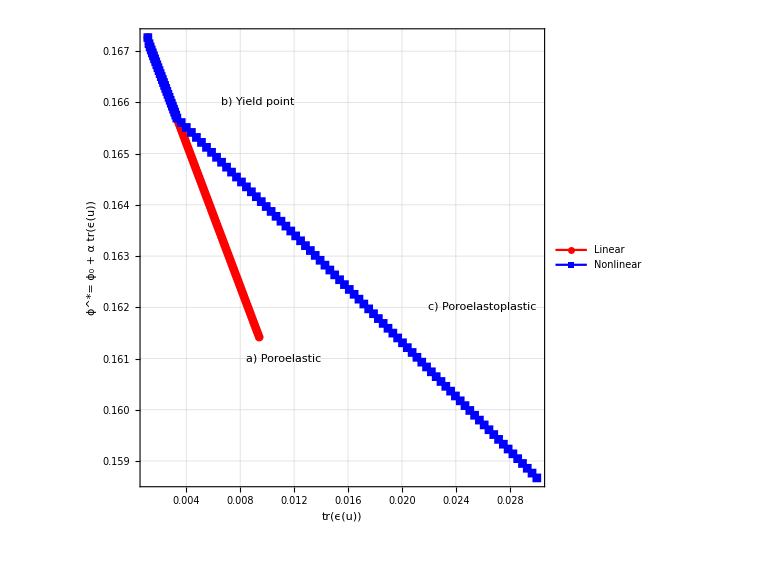

```mathematica
Deformationplot=Show[DeformationplotTemp,txt]
```

```mathematica
Export["ProsityComparison.png",Deformationplot,ImageResolution->200];
```